```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
```

```mathematica
sectionName="NYU-32-X1-1A";

curDir=NotebookDirectory[];
statFile="E:\\04_Cuts and segmentation of serial sections\\"<>sectionName<>"_tiles\\results\\_"<>sectionName<>"_total_villous_regions.csv";



data01=Import[statFile,"Table",FieldSeparators->";"];
dataNames=data01[[1]];
data02=data01[[2;;-1]];
```

```mathematica
data01//Dimensions;
data02//Dimensions;
dataNames
```

{Region,Surface(µm.b2),Perimeter(µm),PerimeterContact(µm),PerimeterFrame(µm),NbIVSinsideRegion,SurfaceIVSinsideRegion(µm.b2),PerimeterIVSinsideRegion(µm),NbGR,SurfaceGR(µm.b2),PerimeterGR(µm)}

```mathematica
areaData=data02[[;;,2]];
```

```mathematica
areaBinSize={50};
distribArea=HistogramDistribution[areaData,areaBinSize];
pdfArea=PDF[distribArea,s];
```

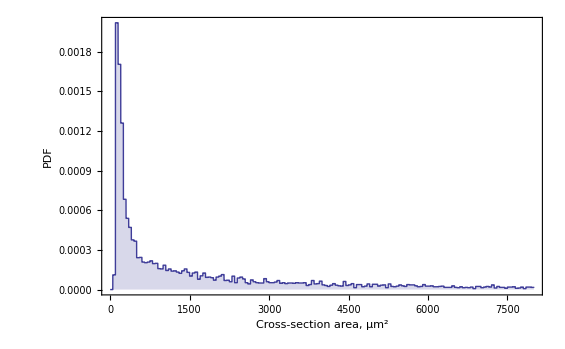

```mathematica
pdfAreaHistogramPlot=DiscretePlot[pdfArea,{s,0,8000},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}]
```

```mathematica
(* Obtaining histogram points *)

distribAreaTempList=HistogramList[areaData,areaBinSize,"PDF"];
binsCenters=Table[(distribAreaTempList[[1,i]]+distribAreaTempList[[1,i+1]])/2,{i,1,Length[distribAreaTempList[[1]]]-1}];
distribAreaList=Transpose[{binsCenters,distribAreaTempList[[2]]}];
```

{A1→96.5439,A2→6.77934×10^6}

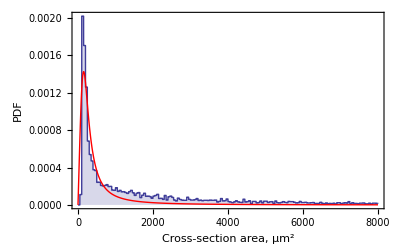

```mathematica
(* Fitting surface distribution *)

fitFunc=A1 s/(A2+s^3);
fitParams={A1,{A2,2*300^3}};
fitVars={s};
fitResult=FindFit[distribAreaList,fitFunc,fitParams,fitVars]

Show[
pdfAreaHistogramPlot,
(*ListPlot[distribLogAreaList,AxesOrigin->{0,0}],*)
Plot[Evaluate[fitFunc/.fitResult],{s,0*0.95*distribAreaList[[1,1]],8000},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red]
]
```

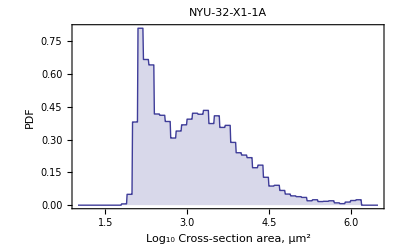

```mathematica
(* A histogram of the distribution of the logarithm of area *)
logAreaData=Log[10,areaData];
logBinSize=0.1;
distribLogArea=HistogramDistribution[logAreaData,{logBinSize}];
pdfLogArea=PDF[distribLogArea,s];
distribLogAreaTempList=HistogramList[logAreaData,{logBinSize},"PDF"];
binsCenters=Table[(distribLogAreaTempList[[1,i]]+distribLogAreaTempList[[1,i+1]])/2,{i,1,Length[distribLogAreaTempList[[1]]]-1}];
distribLogAreaList=Transpose[{binsCenters,distribLogAreaTempList[[2]]}];

pdfLogAreaHistogramPlot= DiscretePlot[pdfLogArea,{s,1,6.5,0.01},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Log_10 Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {4.43095×10^-13, 7.60703×10^-6, 4.39004×10^-13}, is returned.

{A1→0.7557,A2→0.7,σ1→0.33876,σ2→0.741744,y1→1.91907,y2→3.30918}

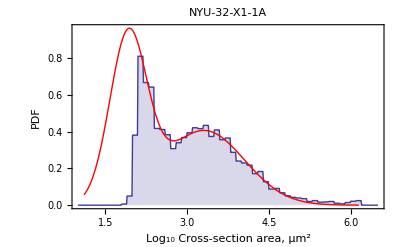

```mathematica
(* Fitting logarithm of surface distribution with two Gaussian *)
fittingInterval={2.2,∞};
fittingData=Select[distribLogAreaList,#[[1]]>=fittingInterval[[1]]&&#[[1]]<=fittingInterval[[2]]&];


fitFunc={A1/(√(2π σ1^2))Exp[-(y-y1)^2/(2 σ1^2)]+A1/(√(2π σ2^2))Exp[-(y-y2)^2/(2 σ2^2)],{A1>0,σ2>0}};
fitParams={{A1,0.7},{A2,0.7},{σ1,0.3},{σ2,0.6},{y1,2.0},{y2,3.4}};
fitVars={y};
fitResult=FindFit[fittingData,fitFunc,fitParams,fitVars]

Show[
pdfLogAreaHistogramPlot,
(*ListPlot[distribLogAreaList,AxesOrigin->{0,0}],*)
Plot[Evaluate[fitFunc/.fitResult],{y,0.6*distribLogAreaList[[1,1]],distribLogAreaList[[-1,1]]},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red],(*AxesOrigin->{0,0},*)PlotRange->All
]
```